```mathematica
Clear["Global`*"]
```

```mathematica
name="/Users/tomoaki/BEM/fish_without_free_surface/result.json"
imported=ImportString[StringReplace[Import[name,"text"],{"NaN"->"null","nan"->"null"}],"JSON"];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
```

/Users/tomoaki/BEM/fish_without_free_surface/result.json

```mathematica
Column[imported[[;;,1]],Background->{{LightOrange,Orange}},Frame->True]
```

bodyA_COM
bodyA_EK
bodyA_EP
bodyA_accel
bodyA_area
bodyA_force
bodyA_pitch
bodyA_roll
bodyA_torque
bodyA_velocity
bodyA_yaw
bodyB_COM
bodyB_EK
bodyB_EP
bodyB_accel
bodyB_area
bodyB_force
bodyB_pitch
bodyB_roll
bodyB_torque
bodyB_velocity
bodyB_yaw
bodyC_COM
bodyC_EK
bodyC_EP
bodyC_accel
bodyC_area
bodyC_force
bodyC_pitch
bodyC_roll
bodyC_torque
bodyC_velocity
bodyC_yaw
cpu_time
simulation_time
wall_clock_time
waterA_E
waterA_EK
waterA_EP
waterA_volume
waterB_E
waterB_EK
waterB_EP
waterB_volume
waterC_E
waterC_EK
waterC_EP
waterC_volume

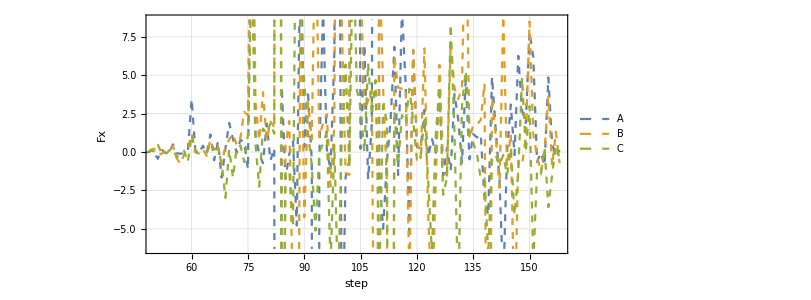

```mathematica
ListPlot[
{getData["bodyA_force",1],
getData["bodyB_force",1],
getData["bodyC_force",1]}
,Joined->True
,PlotStyle->{Dashed,Dashed,Dashed,Thick}
,PlotRange->{{50,Automatic},Automatic}
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["step",FontSize->20,FontFamily->"Times",Italic],Style["Fx",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
,PlotLegends->{"A","B","C"}
]
```

```mathematica
ListPlot[
{Transpose@{getData["time"],getData["bodyA_force",1]},
Transpose@{getData["time"],getData["bodyB_force",1]},
Transpose@{getData["time"],getData["bodyC_force",1]},
Transpose@{getData["time"],Total[Table[getData["body"<>a<>"_force",1],{a,{"A","B","C"}}]]}}
,Joined->True
,PlotStyle->{Dashed,Dashed,Dashed,Thick}
,PlotRange->{{0,4},{-0.4,0.2}}
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["t",FontSize->20,FontFamily->"Times",Italic],Style["F_hydro in x direction",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
,PlotLegends->{"A","B","C","total"}
]
```

Transpose::nmtx: {time,{-11.4685,0.00506198,0.0153827,0.00748724,0.00573001,0.00400182,0.00285008,0.00209939,0.00155259,0.00108001,0.00082996,0.000646737,0.000492061,0.000420075,0.000223022,0.000200923,0.000163225,0.000133857,-0.0000750353,«13»,0.00206594,0.000766994,-0.00427395,0.0152441,0.0149192,0.00604337,0.0053687,-0.0284889,0.125545,0.00913458,0.1437,0.0409891,0.374295,-0.0216903,-0.0498862,-0.0132149,0.0144864,-0.0399285,«108»}}の最初の2個のレベルは転置できません．

Transpose::nmtx: {time,{49995.1,50000,50000,50000,0.00209151,0.00159263,0.0011029,0.000870935,0.000630821,0.000509186,0.000325891,0.000201418,0.000155452,0.000101867,0.0000613559,0.000043439,0.0000358629,-0.0000389606,0.000123291,0.0000242107,«12»,-0.000456785,-0.000210804,0.0122805,0.0111838,0.0174749,0.0153883,-0.0143234,-0.283698,0.0762673,-0.0105155,0.33994,0.0395153,1.35859,0.105847,0.0796968,-0.0346756,0.143258,0.21566,«108»}}の最初の2個のレベルは転置できません．

Transpose::nmtx: {time,{99996.7,100000,100000,100000,-0.02387,0.000227851,-0.00406645,-0.0119868,0.00676543,-0.014961,-0.00897437,-0.0056249,-0.00384227,-0.00259992,-0.0018442,-0.00121448,-0.000876113,-0.000603349,-0.000182525,-0.0002784,«11»,0.0451101,-0.00369972,0.00163497,-0.000298686,0.00454578,0.004174,0.00942198,-0.0102451,-0.238773,0.148344,-0.00970412,0.0312159,-0.0462205,0.618694,0.149554,-0.0162101,-0.0348731,0.0793066,0.0666945,«108»}}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

-Graphics-

```mathematica
ListPlot[
{Transpose@{getData["time"],getData["bodyA_yaw"]},
Transpose@{getData["time"],getData["bodyB_yaw"]},
Transpose@{getData["time"],getData["bodyC_yaw"]}}
,Joined->True
,PlotRange->{{0,4},Automatic}
,BaseStyle->{FontFamily->"Times"}
,AspectRatio->1/2
,GridLines->Automatic
,Frame->True
,FrameLabel->{Style["t",FontSize->20,FontFamily->"Times",Italic],Style["θ",FontSize->20,FontFamily->"Times",Italic]}
,FrameStyle->Directive[FontSize->20,Black,Thickness[0.002]],GridLines->{Table[i,{i,0.,4.,0.2}],Table[i,{i,-1.,1.,0.5}]},GridLinesStyle->Directive[Gray,Dotted]
,ImageSize->600
,PlotLegends->{"A","B","C","total"}
]
```

Transpose::nmtx: {time,{1.73248×10^-9,3.46498×10^-9,5.19751×10^-9,6.93006×10^-9,8.66264×10^-9,1.03952×10^-8,1.21279×10^-8,1.38605×10^-8,1.55932×10^-8,1.73259×10^-8,1.90586×10^-8,2.10185×10^-8,2.41626×10^-8,3.15323×10^-8,5.65795×10^-8,«21»,0.000971871,0.00104539,0.00111412,0.00117522,0.00122525,0.00126011,0.00127493,0.001264,0.00122072,0.00113752,0.00100581,0.000815965,0.000557346,0.000218327,«108»}}の最初の2個のレベルは転置できません．

Transpose::nmtx: {time,{-3.98844×10^-9,-7.97691×10^-9,-1.19654×10^-8,-1.59539×10^-8,-1.99425×10^-8,-2.39311×10^-8,-2.79197×10^-8,-3.19083×10^-8,-3.58969×10^-8,-3.98856×10^-8,-4.38743×10^-8,-4.8386×10^-8,-5.56235×10^-8,-7.25879×10^-8,-1.3024×10^-7,-4.12569×10^-7,«19»,-0.000249991,-0.0000581975,0.00019777,0.000530114,0.000952587,0.00148055,0.00213099,0.00292253,0.00387532,0.00501092,0.00635208,0.00792238,0.00974586,0.0118464,0.014247,«108»}}の最初の2個のレベルは転置できません．

Transpose::nmtx: {time,{-1.2424×10^-9,-2.48489×10^-9,-3.72748×10^-9,-4.97017×10^-9,-6.21295×10^-9,-7.45583×10^-9,-8.6988×10^-9,-9.94188×10^-9,-1.1185×10^-8,-1.24283×10^-8,-1.36717×10^-8,-1.50781×10^-8,-1.73346×10^-8,-2.26248×10^-8,-4.06152×10^-8,-1.2898×10^-7,«19»,-0.00597082,-0.00706313,-0.00830274,-0.00970199,-0.0112733,-0.0130287,-0.0149799,-0.0171375,-0.0195107,-0.0221066,-0.0249295,-0.0279802,-0.0312548,-0.0347439,-0.038431,«108»}}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

-Graphics-